# Performance of Airplanes

Ahmed Salah Hammad Ahmed

#### First year Aerospace engineering

#### SECTION: 1 BN: 4

## لله الفضل و المنة

### This code is prepared on mathematica software, it contains some equations to calculate some important parameters of performance of airplanes whether they are thrust driven or power driven airplanes, with some graphs illustrating those equations. NOTES 1) Some equations are taken directly from references (look at references section) without knowing how to prove them, such as CLmax eq . found it in AOE 3104 course and of course most equations are from Introduction to flight, anderson 2) Most parameters that are used as input in the example cells are assumed or estimated and not real

# Main code

## Thrust driven airplanes

```mathematica
Jet[name_,TA_,W_,W1_,CDo_,CLmax_,e_,b_,s_,rhoinf_,ct_,vcruise_]:=Module[{},
Print[Text@Style[name,Orange,45,Thick,FontFamily->"LM Roman Demi 10",TextAlignment->Center,FontColor->Hue[0.5,0.5,0.5]]];
W0=W;
AR=b^2/s;	k=1/(Pi*e*AR);
A=1/2*rhoinf*v^2*s*CDo;
B=(2*k*W^2)/(rhoinf*v^2*s);
TR=1/2*rhoinf*v^2*s*CDo+(2*k*W^2)/(rhoinf*v^2*s);
PA = TA*v;
PR = 1/2*rhoinf*v^3*s*CDo+(2*k*W^2)/(rhoinf*v*s);
vel=Values[NSolve[TA==TR,v,PositiveReals]];
{vmax,vmin}={Max[vel],Min[vel]};
vstall=√((2W)/(rhoinf*s*CLmax));
Print["v_max = ",SetPrecision[vmax,10]," m/s = ",SetPrecision[vmax,10]*18/5," km/hr", ", v_min = ",SetPrecision[vmin,10]," m/s = ",SetPrecision[vmin,10]*18/5," km/h"];
Print["v_stall = ",SetPrecision[vstall,10]," m/s = ",SetPrecision[vstall,10]*18/5," km/h"];
Print["Maximum thrust = ",Tmax=With[{v=vmax},Evaluate[TR]]," N",", Maximum power = ",Pmax=With[{v=vmax},Evaluate[PR]]," watt"];
jet1=Print[Plot[{TR,TA},{v,0,vmax+50},AxesLabel->{"Velocity (m/s)","Thrust (N)"},PlotLabels->"Expressions",GridLines->Automatic]];
jet2=Print[Plot[{A,B,TR},{v,0,vmax+50},AxesLabel->{"Velocity (m/s)","Thrust (N)"},PlotLabels->"Expressions",GridLines->Automatic,PlotRange->{0,Tmax+0.25*Tmax}]];
jet3=Print[Plot[{PA,PR},{v,0,vmax+50},AxesLabel->{"Velocity (m/s)","Power (Watt)"},PlotLabels->"Expressions",GridLines->Automatic,PlotRange->{0,Pmax+0.25*Pmax}]];
Print["*************************************************************************************************************************"];
gamma=ArcSin[TA/W-1/2 rhoinf*v^2*(W/s)^-1*CDo-(2k)/(rhoinf*v^2)*(W/s)]/Degree;
RC=v*(TA/W-1/2 rhoinf*v^2*(W/s)^-1*CDo-(2k)/(rhoinf*v^2)*(W/s));

{RCmax,g}=FindMaximum[RC,{v,(vmax+vmin)/2}];
g=Values[g];
gammaRCmax=With[{v=g},Evaluate[gamma]];
Print["R/C max = ",SetPrecision[RCmax,10]," m/s",", at v = ",SetPrecision[g,10]," m/s",", at angle of climb = ",gammaRCmax," °"];
jet4=Print[Plot[RC,{v,0,vmax+50},AxesLabel->{"velocity (m/s)","R/C (m/s)"},GridLines->Automatic,PlotRange->{0,RCmax+20}]];


{RCgammamax,u}=FindMaximum[gamma,{v,(vmax+vmin)/2}];
u=Values[u];
gammamax=With[{v=u},Evaluate[gamma]];
Print["Max angle of climb = ",SetPrecision[With[{v=u},gammamax],10]," °, at velocity = ",SetPrecision[u,10]," m/s",", at R/C = ",RCgammamax," m/s"];
Print["*************************************************************************************************************************"];

Habs=-19.867*Log[W/With[{v=vmin},Evaluate[PA]]]*√(2/rhoinf W/s)*((0.7436CDo)/(e*AR)^(3/4))^(1/4);
Print["Absolute ceiling = ",SetPrecision[Habs,10]," m = ",Habs/1000," km"];

a=RCmax;
m=(0-RCmax)/(Habs-0);
Rateclimb=a+m*h;
Hserv=Values[SetPrecision[NSolve[Rateclimb==0.508,h],10]];
Print["Service ceiling = ",Hserv," m = ",Hserv/1000," km"];
jet5=Print[Plot[Rateclimb,{h,0,Habs},PlotRange->{0,RCmax},AxesLabel->{"h (m)","R/C (m/s)"},GridLines->Automatic]];
Print["************************************************************************************************************************"];
t=Integrate[1/Rateclimb,{h,0,Hserv}];
Print["Time of climb to service ceiling = ",SetPrecision[t,10]," seconds"];
jet6=Print[Plot[Rateclimb^-1,{h,0,Habs},AxesLabel->{h,"R/C^-1"},GridLines->Automatic,Filling->Axis]];
Print["*************************************************************************************************************************"];
CLcruise=W/(1/2 rhoinf*vcruise^2*s);
CDcruise=CDo+k*CLcruise^2;
R=2 √(2/(rhoinf*s))*1/ct*CLcruise^(1/2)/CDcruise*(√W0-√W1);
Print["Range = ",SetPrecision[R,10]," m = ",SetPrecision[R,10]/1000," km"];
Endurance=1/ct*CLcruise/CDcruise*Log[W0/W1];
Print["Endurance = ",SetPrecision[Endurance,10]," s = ",SetPrecision[Endurance,10]/3600," h"];Print["*************************************************************************************************************************"];
LDmax=√(1/(4CDo*k));
theta=ArcTan[1/LDmax]/Degree;
Print["(L/D)_max = ",SetPrecision[LDmax,10]];
Print["Minimum θ (angle of gliding) = ",SetPrecision[theta,10]," °"];
]
```

## Power driven airplanes

```mathematica
Prop[name_,PA_,W_,W1_,CDo_,CLmax_,e_,b_,s_,rhoinf_,sfc_,vcruise_,η_]:=Module[{},
Print[Text@Style[name,Orange,45,Thick,FontFamily->"LM Roman Demi 10",TextAlignment->Center,FontColor->Hue[0.5,0.5,0.5]]];
W0=W;
AR=b^2/s;	k=1/(Pi*e*AR);
TR=1/2*rhoinf*v^2*s*CDo+(2*k*W^2)/(rhoinf*v^2*s);
A2=1/2*rhoinf*v^3*s*CDo;
B2=(2*k*W^2)/(rhoinf*v*s);
PR=1/2*rhoinf*v^3*s*CDo+(2*k*W^2)/(rhoinf*v*s);
vel=Values[NSolve[PA==PR,v,PositiveReals]];
{vmax,vmin}={Max[vel],Min[vel]};
vstall=√((2W)/(rhoinf*s*CLmax));
Print["v_max = ",SetPrecision[vmax,10]," m/s = ",SetPrecision[vmax,10]*18/5," km/h", ", v_min = ",SetPrecision[vmin,10]," m/s = ",SetPrecision[vmin,10]*18/5," km/h"];
Print["v_stall = ",SetPrecision[vstall,10]," m/s = ",SetPrecision[vstall,10]*18/5," km/h"];
Print["Maximum thrust = ",Tmax=With[{v=vmax},Evaluate[TR]]," N",", Maximum power = ",Pmax=With[{v=vmax},Evaluate[PR]]," watt"];
Print[Plot[{A2,B2,PR},{v,0,vmax+50},AxesLabel->{"Velocity (m/s)","Power (watt)"},PlotLabels->"Expressions",GridLines->Automatic,PlotRange->{0,Pmax+0.25*Pmax}]];
Print[Plot[{PA,PR},{v,0,vmax+50},AxesLabel->{"Velocity (m/s)","Power (watt)"},PlotLabels->"Expressions",GridLines->Automatic,PlotRange->{0,Pmax+0.25*Pmax}]];
Print["*************************************************************************************************************************"];

RC=(PA-PR)/W;
gamma=ArcSin[RC/v]/Degree;

{RCmax,g}=FindMaximum[RC,{v,(vmax+vmin)/2}];
g=Values[g];
gammaRCmax=With[{v=g},Evaluate[gamma]];
Print["R/C max = ",SetPrecision[RCmax,10]," m/s",", at v = ",SetPrecision[g,10]," m/s",", at angle of climb = ",gammaRCmax," °"];
Print[Plot[RC,{v,0,vmax+50},AxesLabel->{"velocity (m/s)","R/C (m/s)"},GridLines->Automatic,PlotRange->{0,RCmax+20}]];

{RCgammamax,{u}}=FindMaximum[gamma,{v,(vmax+vmin)/2}];
u=Values[u];
gammamax=With[{v=u},Evaluate[gamma]];
Print["Max angle of climb = ",SetPrecision[With[{v=u},gammamax],10]," °, at velocity = ",SetPrecision[u,10]," m/s",", at R/C = ",RCgammamax," m/s"];
Print["*************************************************************************************************************************"];
Habs=-19.867Log[W/PA] √(2/rhoinf*W/s)((0.7436CDo)/(e*AR)^(3/4))^(1/4);
Print["Absolute ceiling = ",SetPrecision[Habs,10]," m = ",Habs/1000," km"];
a=RCmax;
m=(0-RCmax)/(Habs-0);
Rateclimb=a+m*h;
Hserv=Values[SetPrecision[Solve[Rateclimb==0.508,h],10]];
Print["Service ceiling = ",Hserv," m = ",Hserv/1000," km"];
Print[Plot[Rateclimb,{h,0,Habs},PlotRange->{0,RCmax},AxesLabel->{"h (m)","R/C (m/s)"},GridLines->Automatic]];
Print["************************************************************************************************************************"];
t=Integrate[1/Rateclimb,{h,0,Hserv}];
Print["Time of climb to service ceiling = ",SetPrecision[t,10]," seconds"];
Print[Plot[Rateclimb^-1,{h,0,Habs},AxesLabel->{h,"R/C^-1"},GridLines->Automatic,Filling->Axis]];
Print["************************************************************************************************************************"];
LDmax=√(1/(4CDo*k));
CLcruise=W/(1/2 rhoinf*vcruise^2*s);
CDcruise=CDo+CLcruise^2/(Pi*e*AR);
R=Integrate[-η/(w*sfc)*CLcruise/CDcruise,{w,W0,W1}];
Print["Range = ",SetPrecision[R,10]," m = ",SetPrecision[R,10]/1000," km"];
Endurance=η/sfc*CLcruise^(3/2)/CDcruise*√(2*rhoinf *s)*(1/(√W1)-1/(√W0));
Print["Endurance = ",SetPrecision[Endurance,10]," s = ",SetPrecision[Endurance,10]/3600," h"];
Print["************************************************************************************************************************"];
theta=ArcTan[1/LDmax]/Degree;
Print["(L/D)_max = ",SetPrecision[LDmax,10]];
Print["Minimum θ (angle of gliding) = ",SetPrecision[theta,10]," °"];
Print["*************************************************************************************************************************"];
]
```

# Airplanes

F-16

v_max = 681.0353272 m/s = 2451.727178 km/hr, v_min = 41.24075587 m/s = 148.4667211 km/h

v_stall = 69.83986722 m/s = 251.423522 km/h

Maximum thrust = 106000. N, Maximum power = 7.21897×10^7 watt

-Graphics-

-Graphics-

-Graphics-

*************************************************************************************************************************

R/C max = 164.3575833 m/s, at v = {396.0384392} m/s, at angle of climb = {24.5196} °

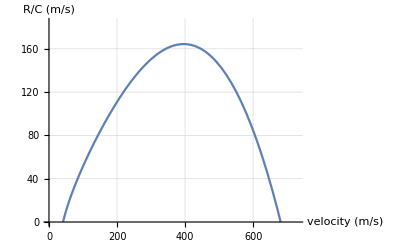

FindMaximum::nrnum: The function value 90.-220.14 ⅈ is not a real number at {v} = {6.70816}.

Max angle of climb = {26.72634672} °, at velocity = {361.1380415} m/s, at R/C = 26.7263 m/s

*************************************************************************************************************************

Absolute ceiling = 1411.20844 m = 1.41121 km

Service ceiling = {{1406.846646}} m = {{1.406846646}} km

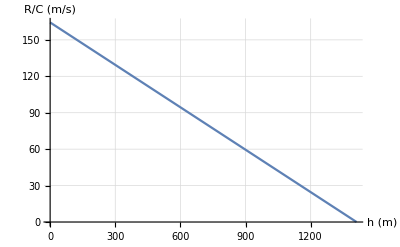

************************************************************************************************************************

Time of climb to service ceiling = {49.62243029} seconds

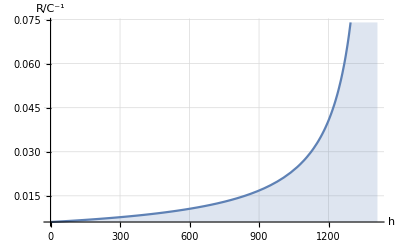

*************************************************************************************************************************

Range = 824933.9327 m = 824.9339327 km

Endurance = 3910.326517 s = 1.08620181 h

*************************************************************************************************************************

(L/D)_max = 13.02482258

Minimum θ (angle of gliding) = 4.390355151 °

```mathematica
Jet["F-16",106*1000,17000*9.8,7390*9.8,0.01,1.5,0.81,9.9568,37.17669984,1.225,0.001988438,257.942]
```

piper pa-28 cherokee

v_max = 102.2549061 m/s = 368.117662 km/h, v_min = 6.37579063 m/s = 22.95284627 km/h

v_stall = 28.8444102 m/s = 103.8398767 km/h

Maximum thrust = 1075.74 N, Maximum power = 110000. watt

-Graphics-

-Graphics-

*************************************************************************************************************************

R/C max = 9.03227241 m/s, at v = {39.45299924} m/s, at angle of climb = {13.2345} °

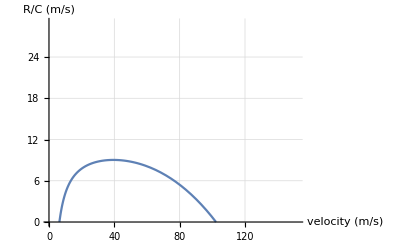

Max angle of climb = 26.73561706 °, at velocity = 12.70301079 m/s, at R/C = 26.7356 m/s

*************************************************************************************************************************

Absolute ceiling = 350.8325288 m = 0.350833 km

Service ceiling = {{331.1007363}} m = {{0.3311007363}} km

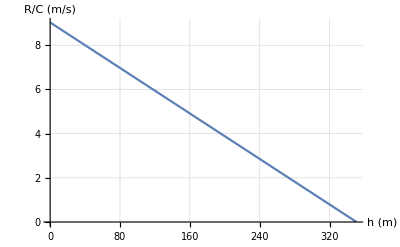

************************************************************************************************************************

Time of climb to service ceiling = {111.7906185} seconds

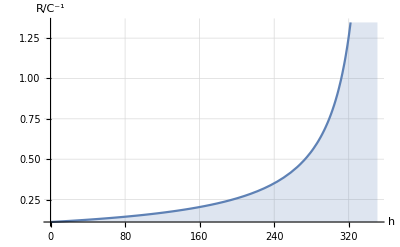

************************************************************************************************************************

Range = 186839.6318 m = 186.8396318 km

Endurance = 3903.216416 s = 1.084226782 h

************************************************************************************************************************

(L/D)_max = 18.36933214

Minimum θ (angle of gliding) = 3.11602402 °

*************************************************************************************************************************

```mathematica
Prop["piper pa-28 cherokee",110000,975*9.8,545*9.8,0.0105,1.25,0.81,9.14,15,1.225,4.25*10^-5,55.5556,0.75]
```